Exercício 1

```mathematica
(*Definição do sistema de equações*)
```

```mathematica
eq1 :=x1''[t]==-ω1^2 x1[t]-ω1^2(x1[t]-x2[t]);
eq2:=x2''[t]==ω2^2(x1[t]-x2[t]);

(*Solução das EDO's usando a função DSolve*)
sols=Assuming[A>0,
DSolve[{eq1,eq2,{x1[0]==0,x2[0]==A},{x1'[0]==0,x2'[0]==0}},{x1[t],x2[t]},t]
]//FullSimplify;
```

```mathematica
(*Defino um vetor de solucões e divido os resultados pela constante A para obter as medidas de x[t] nas unidades corretas*)
```

```mathematica
solsPlot={x1[t],x2[t]}/.sols;
solsPlotUnidadesA=solsPlot/A
```

{{(ω1^2 (-Cosh[(t √(-2 ω1^2-ω2^2-√(4 ω1^4+ω2^4)))/(√2)]+Cosh[(t √(-2 ω1^2-ω2^2+√(4 ω1^4+ω2^4)))/(√2)]))/(√(4 ω1^4+ω2^4)),((-2 ω1^2+ω2^2+√(4 ω1^4+ω2^4)) Cosh[(t √(-2 ω1^2-ω2^2-√(4 ω1^4+ω2^4)))/(√2)]+(2 ω1^2-ω2^2+√(4 ω1^4+ω2^4)) Cosh[(t √(-2 ω1^2-ω2^2+√(4 ω1^4+ω2^4)))/(√2)])/(2 √(4 ω1^4+ω2^4))}}

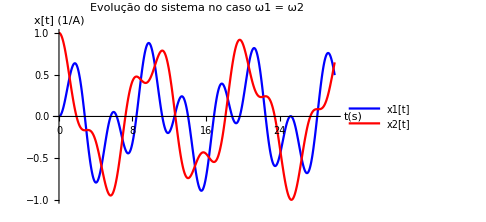

```mathematica
(*Construção dos gráficos das diferentes situações solicitadas*)
visual ={ImageSize->Medium
, LabelStyle->Black
,AxesStyle->{{Medium,Black},{Medium,Black}}
};

(*Caso 1: ω1 == ω2 == 1*)
valores1={ω1->1,ω2->1};
Plot[Evaluate[solsPlotUnidadesA[[1]]/.valores1],{t,0,30}
,Evaluate[visual]
,AxesLabel->{"t(s)","x[t] (1/A)"}
,PlotLabel->"Evolução do sistema no caso ω1 = ω2"
,PlotLegends->{"x1[t]","x2[t]"}
,PlotStyle->{Blue, Red}
]
```

Temos aqui o comportamento típico de um sistema caótico. Uma vez definida as condições iniciais é possível simular a evolução temporal do sistema, mas é impossível prever onde cada oscilador estará em qualquer instante de tempo futuro. O movimento resultante não é periódico.

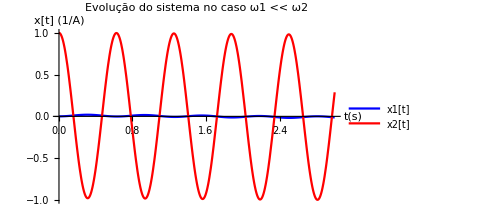

```mathematica
(*Caso 2: ω1 << ω2 *)
valores2={ω1->1,ω2->10};
Plot[Evaluate[solsPlotUnidadesA[[1]]/.valores2],{t,0,3}
,Evaluate[visual]
,AxesLabel->{"t(s)","x[t] (1/A)"}
,PlotLabel->"Evolução do sistema no caso ω1 << ω2"
,PlotLegends->{"x1[t]","x2[t]"}
,PlotStyle->{Blue, Red}]
```

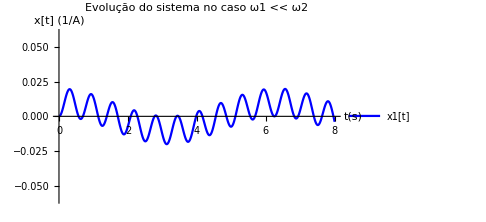

```mathematica
(*Construção de um gráfico específico para o movimento da primeira massa (m1)*)
Plot[Evaluate[solsPlotUnidadesA[[1,1]]/.valores2],{t,0,8}
,Evaluate[visual]
,AxesLabel->{"t(s)","x[t] (1/A)"}
,PlotLabel->"Evolução do sistema no caso ω1 << ω2"
,PlotLegends->{"x1[t]"}
,PlotStyle->{Blue}
,PlotRange->{-0.06,0.06}]
```

Uma vez que as constantes elásticas  k das duas molas são iguais, a condição ω1 << ω2 implica que m1 >> m2. Ou seja, para esse sistema específico seria esperado que a massa m2 oscilasse harmonicamente (com uma frequência dada por ω2) enquanto a massa m1, pelo fato de ser muito mais expressiva, permanecesse aproximadamente em repouso.

De acordo com o primeiro gráfico, tem-se (aproximadamente) as seguintes coordenadas entre dois picos sucessivos associados ao movimento da massa m2 :
{{0.6245888157894736, 0.9836130434557333}, {1.259251644736842, 0.9836130434557333}}
Notemos que a distância entre ambos ao longo do eixo horizontal, a qual define o período de oscilação do objeto, é  cerca de 0.634 s. Em outras palavras, temos uma estimativa para o período de oscilação dessa massa. Mas, pela definição de período, sabemos que T2=2π/ω2 =0.628 s (dado que ω2 = 10 Hz). 
A dinâmica observada para a massa m2 está, portanto, completamente dentro das expectativas.

A dinâmica da massa m1 também está sendo descrita conforme esperado. No segundo gráfico construído é possível notar pequenas oscilações em torno da posição x1 = 0, mas que também evoluem no tempo de maneira periódica com período de aproximadamente 2π/ω1=6.28 (dado que ω1 = 1 Hz)

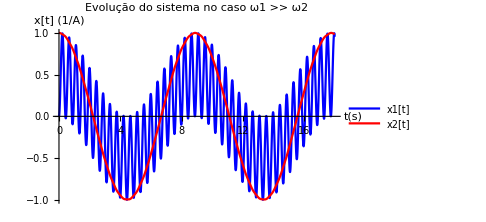

```mathematica
(*Caso 3: ω1 >> ω2*)
valores3={ω1->10,ω2->1};
Plot[Evaluate[solsPlotUnidadesA[[1]]/.valores3],{t,0,18}
,Evaluate[visual]
,AxesLabel->{"t(s)","x[t] (1/A)"}
,PlotLabel->"Evolução do sistema no caso ω1 >> ω2"
,PlotLegends->{"x1[t]","x2[t]"}
,PlotStyle->{Blue, Red}
]
```

No caso ω1 >> ω2 temos uma condição exatamente oposta à do caso anterior: m1 << m2. Nessa situação esperamos um comportamento no qual a massa m2 oscile harmonicamente com período aproximadamente igual a T2 = 2π/ω2 enquanto a massa m1 seja “arrastada” em conjunto com m2.
Perceba que tanto no caso anterior quanto nesse caso particular é esperado que m2 oscile com período T2, mas é importante destacar que as razões são distintas. No caso inicial essa oscilação ocorre devido ao fato de que m1>>m2 (e, portanto, m1 poderia ser visto como uma espécie de parede na qual m2 estava apoiada). Agora essa oscilação ocorre já que, pelo fato de termos m2>>m1 e m2 ser a massa externa do sistema, seu movimento deve ser predominante sobre o movimento da massa m1 acoplada.

Novamente, é justamente esse o padrão que observamos no gráfico construído. Enquanto m1 oscila rapidamente em torno da posição de equilíbrio ao passo que acompanha o movimento da massa m2, os primeiros dois picos sucessivos associados à curva x2[t] têm coordenadas {{0., 0.9951995424154843}, {8.885279605263161, 1.006790183394812}}. Isso implica um período T2 = 8.88 s, que é um resultado um pouco discrepante em relação ao valor de 2π, mas ainda aceitável dadas as características da dinâmica não trivial associadas ao sistema em estudo.

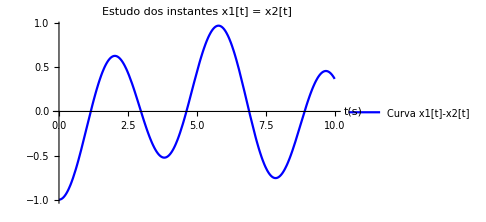

```mathematica
(*Determinação dos instantes em que x1[t] = x2[t]*)
values={A->1,ω1->1,ω2->1};
Plot[Evaluate[(solsPlot[[1,1]]-solsPlot[[1,2]])/.values],{t,0,10}
,Evaluate[visual]
,AxesLabel->{"t(s)"}
,PlotLabel->"Estudo dos instantes x1[t] = x2[t]"
,PlotLegends->{"Curva x1[t]-x2[t]"}
,PlotStyle->{Blue}
]
```

```mathematica
(*A função x1[t]-x2[t] se anula quando x1[t]= x2[t]. Portanto, ao encontrar as 4 primeiras raízes dessa função, encontramos também os 4 primeiros instantes em que a igualdade é verificada*)
raizes={{1.1081414473684217,0.001984178850573226},{3.0893640350877196,0.013418329926023098},{4.600466008771932,0.024852481001473414},{6.883908991228072,0.013418329926023098}};

Table[
FindRoot[Evaluate[(solsPlot[[1,1]]-solsPlot[[1,2]])/.values],{t,raizes[[i,1]]}],{i,Length[raizes]}
]
```

{{t→1.15211},{t→2.975},{t→4.62207},{t→6.89855}}

Exercício 2

```mathematica
(*Definição dos pares oordenados de dados*)
```

```mathematica
Temperaturas={-8,-5,0,5,10,15,18,20,30,40,50,60,70,80,100}(*.baC*);

sigmas={77.0,76.4,75.6,74.9,74.22,73.49,73.05,72.75,71.18,69.56,67.91,66.18,64.4,62.6,58.9}(*dyne/cm*);

listaTempSigma={Temperaturas,sigmas};
plotDados=listaTempSigma//Transpose
```

{{-8,77.},{-5,76.4},{0,75.6},{5,74.9},{10,74.22},{15,73.49},{18,73.05},{20,72.75},{30,71.18},{40,69.56},{50,67.91},{60,66.18},{70,64.4},{80,62.6},{100,58.9}}

```mathematica
(*Obtenção dos parâmetros de ajuste linear*)
Fit[plotDados,{1,T},T]
```

75.8655-0.164624 T

Portanto, os parâmetros a e b têm, aproximadamente, os seguintes valores: 75.87  dyne/cm e b=-0.1646  (dyne)/(cm .baC)

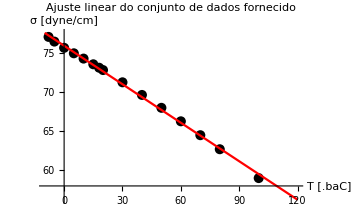

```mathematica
(*Construção do gráfico de visualização do conjunto de dados*)
Pontos=ListPlot[
plotDados
,Evaluate[visual]
,PlotStyle->{Black,PointSize[0.02]}
];

σ[T_]:=a+b T;
values={a->75.87,b-> -0.1646};
Ajuste=Plot[
σ[T]/.values,{T,-10,120}
,Evaluate[visual]
,PlotStyle->Red
];

Show[
Pontos
,Ajuste
,AxesLabel->{"T [.baC]","σ [dyne/cm]"}
,PlotLabel->"Ajuste linear do conjunto de dados fornecido"
,PlotRange->All
]
```

Exercício 3

```mathematica
(*Construção / Solução do sistema de equações diferenciais*)
Clear[x,y]
eqx:=m x''[t]==-(k x[t])/((√(x[t]^2+y[t]^2))^(1+β));
eqy:=m y''[t]==(-k y[t])/((√(x[t]^2+y[t]^2))^(1+β));
```

```mathematica
(*Análise do movimento circular uniforme (MCU)*)
```

O movimento da partícula será circular se a força resultante (que, nesse caso, é simplesmente a força atrativa de um corpo central) for a resultante centrípeta. Impondo essa condição de igualdade para β = 2, temos:

k/a^2=(m v^2)/a→v=√(k/(m a)), sendo a o raio da trajetória circular.

É importante lembrar, entretanto, que essa é a condição que o modulo da velocidade deve satisfazer, ou seja |v⃗|=√(v_x^2+v_y^2). 
Para termos um movimento circular, então, basta impor (por exemplo) v_x[t=0]=0 e v_y[t=0]=√(k/(m a)). Desse modo temos que |v⃗[t=0]|satisfaz a condição de movimento circular e, consequentemente, uma vez que estamos lidando com um sistema conservativo, concluimos que o movimento da partícula será circular para todo instante de tempo.

Além disso, para garantir que o raio do movimento seja efetivamente a quantidade r descrita nas expressões anteriores, podemos impor x[t=0]=a e y[t=0]=0.

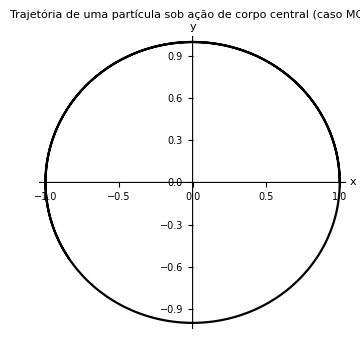

```mathematica
(*Solução numérica do sistema de equações*)
valuesAux={m->1,k->1,a->1,β->2};
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== 0,y'[0]== √(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

solsPlot={x[t],y[t]}/.sols;

ParametricPlot[
Evaluate[solsPlot]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central (caso MCU)"
,AxesLabel->{"x","y"}
,PlotStyle->Black
]
```

```mathematica
(*Faço uma análise da mesma configuração do sistema, mas para diferentes condições iniciais*)
(* 0) x[0]= a / y[0]= 0 / Subscript[v, x][0]= 0 / Subscript[v, y][0]= √(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== 0,y'[0]== √(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva0=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Black}
,PlotLegends->{"MCU"}
];
(* 1) x[0]= 0 / y[0]= a / Subscript[v, x][0]= -1/(√2)√(k/(m a)) / Subscript[v, y][0]= 1/(√2)√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== 0,y[0]== a,x'[0]==-1/(√2)√(k/(m a)) ,y'[0]==1/(√2)√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva1=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Green}
,PlotLegends->{"x[0] = 0, y[0] = a, v_x[0] = -(1/√2)√(k/(m a)) , v_y[0] = (1/√2)√(k/(m a))"}
];

(* 2) x[0]= a / y[0]= 0 / Subscript[v, x][0]=1/(√2)√(k/(m a)) / Subscript[v, y][0]=1/(√2)√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== 1/(√2)√(k/(m a)),y'[0]==1/(√2)√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];
curva2=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols],{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,PlotStyle->{Red}
,PlotLegends->{"x[0] = a, y[0] = 0, v_x[0] = (1/√2)√(k/(m a)) , v_y[0] = (1/√2)√(k/(m a))"}
,PlotRange->All
];
(* 3) x[0]= a / y[0]= 0 / Subscript[v, x][0]=-1/(√2)√(k/(m a)) / Subscript[v, y][0]=1/(√2)√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== -1/(√2)√(k/(m a)),y'[0]==1/(√2)√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];
curva3=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols],{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,PlotStyle->{Orange}
,PlotLegends->{"x[0] = a, y[0] = 0, v_x[0] = -(1/√2)√(k/(m a)) , v_y[0] = (1/√2)√(k/(m a))"}
,PlotRange->All
];
(* 4) x[0]= -a / y[0]= 0 / Subscript[v, x][0]= -1/(√2)√(k/(m a)) / Subscript[v, y][0]= -1/(√2)√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== -a,y[0]== 0,x'[0]==  -1/(√2)√(k/(m a)),y'[0]==  -1/(√2)√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva4=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Purple}
,PlotLegends->{"x[0] = -a, y[0] = 0, v_x[0] = -(1/√2)√(k/(m a)) , v_y[0] = -(1/√2)√(k/(m a))"}
];
```

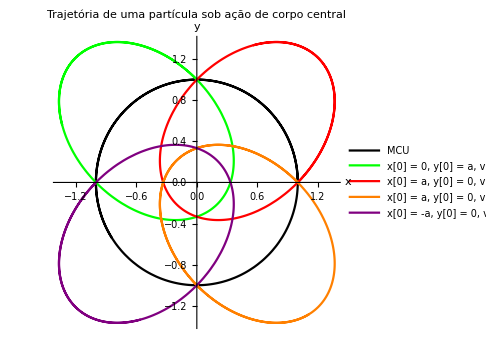

```mathematica
Show[
curva0
,curva1
,curva2
,curva3
,curva4
,PlotRange->All
]
```

```mathematica
(*Estudo do caso β=3*)
```

Nessas condições a nova velocidade necessária para a reprodução de um movimento circular seria

k/a^3=(m v^2)/a→v=1/a √(k/m), sendo a o raio da trajetória circular.

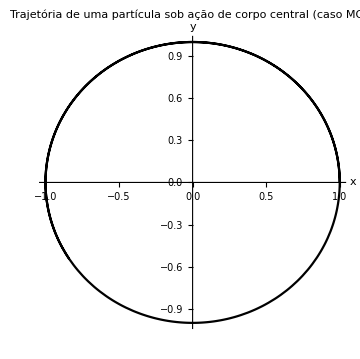

```mathematica
(*Construo o gráfico de verificação de trajetória*)
valuesAux={m->1,k->1,a->1,β->3};
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== 0,y'[0]== (1/a)√(k/m)}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva0=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central (caso MCU)"
,AxesLabel->{"x","y"}
,PlotStyle->Black
]
```

```mathematica
(*Ainda para β=3, faço uma invetigação de trajetória para velocidades iniciais distintas*)
(* 0) x[0]= -a / y[0]= 0 / Subscript[v, x][0]= 0 / Subscript[v, y][0]= √5 √(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== -a,y[0]== 0,x'[0]==  0,y'[0]==  √5 √(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva0=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Blue}
,PlotLegends->{"x[0] = -a, y[0] = 0, v_x[0] = 0, v_y[0] = √5√(k/(m a))"}
];
(* 1) x[0]= -a / y[0]= 0 / Subscript[v, x][0]= √2 √(k/(m a)) / Subscript[v, y][0]= √3 √(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== -a,y[0]== 0,x'[0]==  √2 √(k/(m a)),y'[0]== √3 √(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva1=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Green}
,PlotLegends->{"x[0] = -a, y[0] = 0, v_x[0] = √2√(k/(m a)), v_y[0] = √3√(k/(m a))"}
];
(* 2) x[0]= a / y[0]= 0 / Subscript[v, x][0]= √(k/(m a)) / Subscript[v, y][0]= -√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]==  √(k/(m a)),y'[0]==  -√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,10}];

curva2=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,10}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Red}
,PlotLegends->{"x[0] = a, y[0] = 0, v_x[0] = √(k/(m a)), v_y[0] = -√(k/(m a))"}
];
(* 3) x[0]= a / y[0]= 0 / Subscript[v, x][0]= 0 / Subscript[v, y][0]= 1.42/(√2)√(k/(m a))*)
sols=NDSolve[
{eqx,eqy,x[0]== a,y[0]== 0,x'[0]== 0,y'[0]==  1.42/(√2)√(k/(m a))}/.valuesAux,{x[t],y[t]},{t,0,100}];

curva3=ParametricPlot[
Evaluate[{x[t],y[t]}/.sols]
,{t,0,100}
,Evaluate[visual]
,PlotLabel->"Trajetória de uma partícula sob ação de corpo central"
,AxesLabel->{"x","y"}
,PlotStyle->{Orange}
,PlotLegends->{"x[0] = a, y[0] = 0, v_x[0] = 0, v_y[0] = (1.42/√2)√(k/(m a))"}
];
```

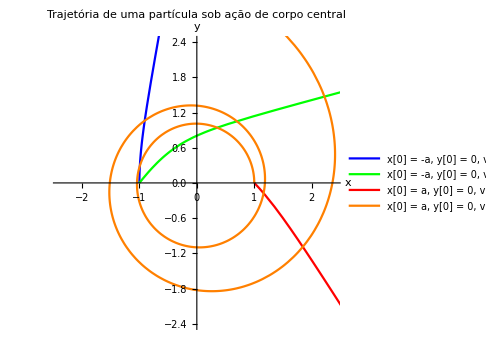

```mathematica
Show[
curva0,
curva1,
curva2,
curva3,
PlotRange->{{-2.4,2.4},{-2.4,2.4}}
]
```

No caso de velocidades iniciais que não satisfazem as condições de movimento circular/elíptico iniciais, a trajetória não se fecha. Em particular, para as escolhas de velocidade inicial feitas nessa atividade, a partícula deixa o campo de atuação da massa central e passa a se mover até o infinito (tornando-se, portanto, uma partícula livre).